# Computer Mathematics Course Work

Dmytro Zakharov

Kharkiv Karazin National University, Applied Mathematics

Variant 13

## 1. Introduction to Wolfram Mathematica

### 1.1. Arithmetical Operations

Task: Find the value of expression (0.134+0.05)/((18+1/6)-(1+11/14)-2/15 (2+6/7))

```mathematica
Clear[Answer]
Answer = (0.134+0.05)/((18+1/6)-(1+11/14)-2/15(2+6/7));
Print["Answer is ", Answer]
```

Answer is 0.0115

### 1.2. Evaluating expression containing solely elementary functions

Task: Find the value of expression

```mathematica
Clear[y,Answer]
y=1/3 Cos[1/Tan[3]]+1/5 (Sin[5 Sqrt[2]])^2/Cos[10 ⅇ^3];
Answer = N[y];
Print["Answer is ", Answer]
```

Answer is 0.350611

## 2. Algebraic Evaluation

### 2.1. Algebraic Manipulations

Task: Simplify expression

```mathematica
Clear[a,b,c,n,Result]
Result=Simplify[((2 a^2(b+c)^(2n)-1/2)/(a n^2-a^3-2 a^2-a))/((2a(b+c)^n-1)/(a^2 c-a(n c-c)))];
Print["Result is ", Result]
```

Result is -(c (1+2 a (b+c)^n))/(2 (1+a+n))

### 2.2. Finding values of algebraic expressions

Task: Calculate  for

```mathematica
Remove[a,b,Answer]
Expr = (Sqrt[a b]-(a b)/(a+Sqrt[a b]))/((Surd[a b,4]-Sqrt[b])/(a-b));
Answer = Simplify[Expr/.{a->8,b->2}];
Print["The answer is ", Answer]
```

The answer is 8 (2+√2)

### 2.3. Solving equations

Task: Solve equation  for

```mathematica
Clear[a,x]
Solve[1/a+1/(a+x)+1/(a+2 x)==0,x]
```

{{x→1/2 (-3 a-√3 a)},{x→1/2 (-3 a+√3 a)}}

## 3. Elements of Analytical Geometry

### 3.1. Operating with vectors

Task: For vectors  determine whether  and  are collinear. Find lengths of vectors  and  and angle between them. Draw vectors  and .

```mathematica
Clear[a,b,c1,c2]
a={-2,7,-1};
b={-3,5,2};
c1=2 a+3 b;
c2=3a+2b;
ratio=c1/c2;
Print["Ratio is ", ratio]
```

Ratio is {13/12,29/31,4}

We thus conclude that  and  are not collinear.

```mathematica
LengthOfA=Norm[a];
LengthOfB=Norm[b];
AngleAB=(N[VectorAngle[a,b]] 180)/π;
Print["Length of a is ", LengthOfA," and length of b is ", LengthOfB]
Print["Angle between a and b (in degrees) is ", AngleAB]
```

Length of a is 3 √6 and length of b is √38

Angle between a and b (in degrees) is 30.577

```mathematica
z={0,0,0}
Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{z,a}],Arrow[{z,b}]},Axes->True,AxesLabel->{"x","y","z"}]
```

{0,0,0}

-Graphics3D-

### 3.2. Geometric calculations in Triangle

Task: Given triangle with vertices , find its sides, angles and area.

```mathematica
A1 = {6,2,-3}; A2 = {6,3,-2}; A3={7,3,-3};
ListPlot3D[{A1,A2,A3},BoxRatios->Automatic,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

```mathematica
A1A2=A2-A1; A1A3=A3-A1; A2A3=A3-A2;
LengthA1A2=Norm[A1A2];LengthA1A3=Norm[A1A3];LengthA2A3=Norm[A2A3];
angleA1=VectorAngle[A1A2,A1A3];angleA2=VectorAngle[-A1A2,A2A3]; angleA3=VectorAngle[A1A3,A2A3];
Print["Lengths of sides A_1A_2, A_1A_3, and A_2A_3 are ", LengthA1A2,", ",LengthA1A3,", ",LengthA2A3]
Print["Angles A_1, A_2, and A_3 are ", angleA1, ", ", angleA2,", ", angleA3]
```

Lengths of sides A_1A_2, A_1A_3, and A_2A_3 are √2, √2, √2

Angles A_1, A_2, and A_3 are π/3, π/3, π/3

```mathematica
S=1/2 Norm[Cross[A1A2,A1A3]];
Print["Area of triangle is ", S]
```

Area of triangle is (√3)/2

### 3.3. Calculations in Tetrahedron

Task. Given Tetrahedron with vertices , find its volume, height  from vertex  on side . Display this tetrahedron, height  and point .

```mathematica
A1={1,1,2};A2={-1,1,3};A3={2,-2,4};A4={-1,0,-2};
A1A2=A2-A1;A1A3=A3-A1;A1A4=A4-A1;
V=1/6 Abs[Det[{A1A2,A1A3,A1A4}]];
n=-Cross[A1A2,A1A3];
S=1/2 Norm[n];
h=(3 V)/S;
B=A4-n/(2S)h;
graph1=Graphics3D[{Thickness[0.01],Line[{A1,A2,A3,A1,A4,A2,A3,A4}]},AxesLabel->{"x","y","z"},Axes->True,BaseStyle->{Blue,Opacity[.7]}];
graph2=ListPointPlot3D[{B}->{"Intersection"},PlotStyle->{Directive[PointSize[0.03],Red]}];
graph3=Graphics3D[{Thickness[0.01],{Dashed,Red,Line[{A4,B}]}}];
graph4=Graphics3D[{Opacity[0.3],Gray,InfinitePlane[{A1,A2,A3}]}];
Show[graph1,graph2,graph3,graph4]
```

-Graphics3D-

## 4. Matrix Calculations

### 4.1. Working with matrices

Task: Given matrices , find  where  is an identity matrix. Find inverse matrix . Find . Find sum and difference of . Find  and , find difference between these values. Solve matrix equation  with respect to .

```mathematica
A={{1,2,1},{0,2,0},{-1,1,1}};
B={{1,1,2},{0,2,1},{1,-1,0}};
M=2*A.A+3 A+5 IdentityMatrix[3];
Print["Matrix polynomial equals ",M//MatrixForm]
```

Matrix polynomial equals (8 | 20 | 7
0 | 19 | 0
-7 | 5 | 8)

```mathematica
InverseA=Inverse[A];
Print["Inverse of matrix A is ", InverseA//MatrixForm]
```

Inverse of matrix A is (1/2 | -1/4 | -1/2
0 | 1/2 | 0
1/2 | -3/4 | 1/2)

```mathematica
DetA=Det[A];
Print["det(A) = ", DetA]
```

det(A) = 4

```mathematica
Print["Sum of matrices A and B is ", (A+B)//MatrixForm]
Print["Difference between matrices A and B is ", (A-B)//MatrixForm]
```

Sum of matrices A and B is (2 | 3 | 3
0 | 4 | 1
0 | 0 | 1)

Difference between matrices A and B is (0 | 1 | -1
0 | 0 | -1
-2 | 2 | 1)

```mathematica
MatProduct=A.B;
ElemProduct=A*B;
Print["Matrix product of A and B is ", MatProduct//MatrixForm]
Print["Elementwise product of A and B is ", ElemProduct//MatrixForm]
Print["Difference between corresponding products is", (MatProduct-ElemProduct)//MatrixForm]
```

Matrix product of A and B is (2 | 4 | 4
0 | 4 | 2
0 | 0 | -1)

Elementwise product of A and B is (1 | 2 | 2
0 | 4 | 0
-1 | -1 | 0)

Difference between corresponding products is(1 | 2 | 2
0 | 0 | 2
1 | 1 | -1)

```mathematica
X=InverseA.B;
Print["Solution to matrix equation AX=B w/ respect to X is ", X//MatrixForm]
```

Solution to matrix equation AX=B w/ respect to X is (0 | 1/2 | 3/4
0 | 1 | 1/2
1 | -3/2 | 1/4)

### 4.2. Working with both matrices and vectors

Task: Given matrices  calculate  and . Solve equation  with respect to  using inverse matrix and Cramer’s rule. For each row and column of  find sum of elements. For matrix  find max and min elements.

```mathematica
A={{0,2,3},{4,1,0},{2,-1,-2}};
B={{1,2,0},{3,0,-1},{2,1,-1}};
x={2,4,-1};
y=(A-B).(A-B).x;
Print["Vector y is ", MatrixForm[y]]
z=(A.B-B.A).x;
Print["Vector z is ", MatrixForm[z]]
```

Vector y is (-16
-7
-3)

Vector z is (12
34
-25)

To solve equation  we firstly use inverse matrix, that is, :

```mathematica
u=Inverse[A].x;
Print["Solution to Au=x w/ respect to u is ",MatrixForm[u]]
```

Solution to Au=x w/ respect to u is (-3/2
10
-6)

Now, using Cramer’s rule:

```mathematica
A1=Join[Transpose[{x}],A[[All,2;;3]],2];
Print["After putting vector x to the first column we get ",MatrixForm[A1]]
```

After putting vector x to the first column we get (2 | 2 | 3
4 | 1 | 0
-1 | -1 | -2)

```mathematica
A2=Join[A[[All,1;;1]],Transpose[{x}],A[[All,3;;3]],2];
Print["After putting vector x to the second column we get ",MatrixForm[A2]]
```

After putting vector x to the second column we get (0 | 2 | 3
4 | 4 | 0
2 | -1 | -2)

```mathematica
A3=Join[A[[All,1;;2]],Transpose[{x}],2];
Print["After putting vector x to the third column we get ",MatrixForm[A3]]
```

After putting vector x to the third column we get (0 | 2 | 2
4 | 1 | 4
2 | -1 | -1)

```mathematica
cramerU={Det[A1],Det[A2],Det[A3]}/Det[A];
Print["Vector u calculated using Cramer's rule is ", cramerU//MatrixForm]
```

Vector u calculated using Cramer's rule is (-3/2
10
-6)

```mathematica
Print["Sum of columns of matrix A is ",Total[A]]
Print["Sum of rows of matrix A is ", Total[A,{2}]]
Print["Max element of B is ",Max[B]]
Print["Min element of B is ",Min[B]]
```

Sum of columns of matrix A is {6,2,1}

Sum of rows of matrix A is {5,5,-1}

Max element of B is 3

Min element of B is -1

### 4.3. Creating matrices

Task 1: Generate a one-dimensional array  of size  containing random real numbers. Sort it in descending order and convert to a matrix . Create matrix  of size  containing ’s. Generate matrix  of size , elements  of which are calculated according to formula . Generate diagonal array  with elements of diagonal . Calculate  where  is identity matrix of size .

```mathematica
a=RandomReal[1,16];
Print["Random list a is ",a]
aSorted=Sort[a,Greater];
Print["Sorted list a is ",aSorted]
A=ArrayReshape[aSorted,{4,4}];
Print["Reshaped list a as a matrix A is ", A//MatrixForm]
B=ConstantArray[5,{4,4}];
Print["Matrix B is ",B//MatrixForm]
F=Table[i^2-j^2,{i,1,4},{j,1,4}];
Print["Matrix F is ",F//MatrixForm]
G=DiagonalMatrix[{1,-1,2,-2}];
Print["Matrix G is ", G//MatrixForm];
M=A+B-F-G+IdentityMatrix[4]-3;
Print["Expression A+B-F-G+E-3 equals ",M//MatrixForm]
```

Random list a is {0.35427,0.699043,0.911459,0.477622,0.589589,0.200876,0.154128,0.557092,0.580649,0.758855,0.807006,0.961893,0.419614,0.473136,0.863843,0.452541}

Sorted list a is {0.961893,0.911459,0.863843,0.807006,0.758855,0.699043,0.589589,0.580649,0.557092,0.477622,0.473136,0.452541,0.419614,0.35427,0.200876,0.154128}

Reshaped list a as a matrix A is (0.961893 | 0.911459 | 0.863843 | 0.807006
0.758855 | 0.699043 | 0.589589 | 0.580649
0.557092 | 0.477622 | 0.473136 | 0.452541
0.419614 | 0.35427 | 0.200876 | 0.154128)

Matrix B is (5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5)

Matrix F is (0 | -3 | -8 | -15
3 | 0 | -5 | -12
8 | 5 | 0 | -7
15 | 12 | 7 | 0)

Matrix G is (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | -2)

Expression A+B-F-G+E-3 equals (2.96189 | 5.91146 | 10.8638 | 17.807
-0.241145 | 4.69904 | 7.58959 | 14.5806
-5.44291 | -2.52238 | 1.47314 | 9.45254
-12.5804 | -9.64573 | -4.79912 | 5.15413)

Task 2. Create matrix  elements of which are calculated according to relation  where . Add to  a column containing . Then, between columns 1 and 2 insert another column containing ’s.

```mathematica
x={-3,0,1,2,5};y={-5,0,-4,1,3};
Z=Table[(x[[i]])^2-(y[[j]])^2,{i,1,5},{j,1,5}];
Print["Initial matrix Z is ", Z//MatrixForm]
```

Initial matrix Z is (-16 | 9 | -7 | 8 | 0
-25 | 0 | -16 | -1 | -9
-24 | 1 | -15 | 0 | -8
-21 | 4 | -12 | 3 | -5
0 | 25 | 9 | 24 | 16)

```mathematica
joinedZ=Join[Z,Transpose[{{1,2,3,4,5}}],2];
Print["After adding columns {1,2,3,4,5} to Z we get ",joinedZ//MatrixForm]
```

After adding columns {1,2,3,4,5} to Z we get (-16 | 9 | -7 | 8 | 0 | 1
-25 | 0 | -16 | -1 | -9 | 2
-24 | 1 | -15 | 0 | -8 | 3
-21 | 4 | -12 | 3 | -5 | 4
0 | 25 | 9 | 24 | 16 | 5)

```mathematica
joinedWithOnesZ=Join[joinedZ[[All,1;;1]],Transpose[{ConstantArray[1,5]}],joinedZ[[All,3;;6]],2];
Print["After adding column {1,1,1,1,1} between first and second solumns we get ", joinedWithOnesZ//MatrixForm]
```

After adding column {1,1,1,1,1} between first and second solumns we get (-16 | 1 | -7 | 8 | 0 | 1
-25 | 1 | -16 | -1 | -9 | 2
-24 | 1 | -15 | 0 | -8 | 3
-21 | 1 | -12 | 3 | -5 | 4
0 | 1 | 9 | 24 | 16 | 5)

## 5. Solving equations and systems of equations

### 5.1. Solving equations

Task. Solve equation  w/ respect to .

```mathematica
Clear[x,a]
Solve[(Sqrt[1+x^2/a^2]-x/a)/(Sqrt[1+x^2/a^2]+x/a)==1/4,x]
```

{{x→(3 a)/4}}

### 5.2. Solving system of linear equations

Task. Solve system of linear equations  given my matrix  and vector .

#### 5.2.1. Inverse matrix method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
x=Inverse[A].b;
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.2. Using Solve function

```mathematica
Solve[x1+2x2-3x3+4x4-x5==-1&&2x1-x2+3x3-4x4+2x5==8&&3x1+x2-x3+2x4-x5==3&&4x1+3x2+4x3+2x4+2x5==-2&&x1-x2-x3+2x4-3x5==-3,{x1,x2,x3,x4,x5}]
```

{{x1→2,x2→0,x3→-2,x4→-2,x5→1}}

#### 5.2.3. Using LinearSolve function

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
x=LinearSolve[A,b];
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.4. Using Cramer’s method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
A1=Join[Transpose[{b}],A[[All,2;;5]],2];
A2=Join[A[[All,1;;1]],Transpose[{b}],A[[All,3;;5]],2];
A3=Join[A[[All,1;;2]],Transpose[{b}],A[[All,4;;5]],2];
A4=Join[A[[All,1;;3]],Transpose[{b}],A[[All,5;;5]],2];
A5=Join[A[[All,1;;4]],Transpose[{b}],2];
x={Det[A1],Det[A2],Det[A3],Det[A4],Det[A5]}/Det[A];
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.5. Using RowReduce method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
RowReduce[Join[A,Transpose[{b}],2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 2
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -2
0 | 0 | 0 | 1 | 0 | -2
0 | 0 | 0 | 0 | 1 | 1)

### 5.3. Solving non-linear equations

Task. Solve system of non-linear equations  and .

```mathematica
Clear[x,y]
Solve[x^3+y^3==35&&x y(x+y) == 30,{x,y},Reals]
```

{{x→2,y→3},{x→3,y→2}}

## 6. Functions and their plots

### 6.1. Plotting function by a points list

Task. Plot function  and its table of values. Plot ListPlot based on this table.

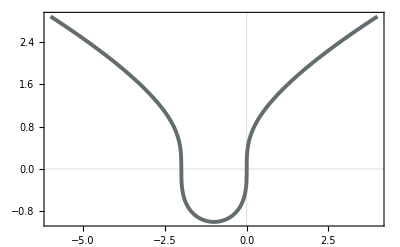

```mathematica
Remove[x,y];
y[x_]=CubeRoot[x(x+2)];
p1=Plot[y[x],{x,-6,4},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

```mathematica
points=Table[{x,N[y[x]]},{x,-6,4,0.5}];
points//TableForm
```

-6. | 2.8845
-5.5 | 2.68005
-5. | 2.46621
-4.5 | 2.2407
-4. | 2.
-3.5 | 1.73801
-3. | 1.44225
-2.5 | 1.07722
-2. | 0.
-1.5 | -0.90856
-1. | -1.
-0.5 | -0.90856
0. | 0.
0.5 | 1.07722
1. | 1.44225
1.5 | 1.73801
2. | 2.
2.5 | 2.2407
3. | 2.46621
3.5 | 2.68005
4. | 2.8845

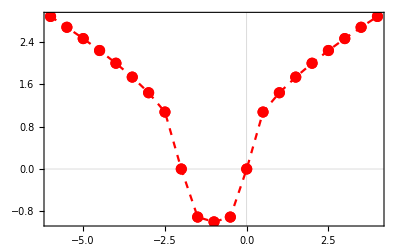

```mathematica
p2=ListPlot[points,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Red,Dashed},PlotTheme->"Scientific"]
```

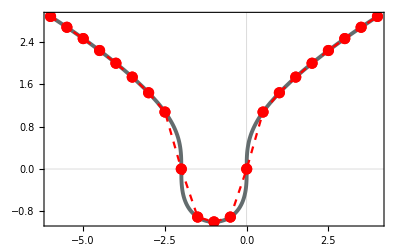

```mathematica
Show[p1,p2]
```

### 6.2. Building polynomial plot

Task. Plot polynomial .

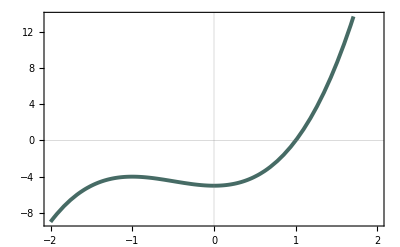

```mathematica
Remove[x,y];
y[x_]=-5+3 x^2+2 x^3;
Plot[y[x],{x,-2,2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.3. Build arbitrary explicitly defined function

Task. Plot

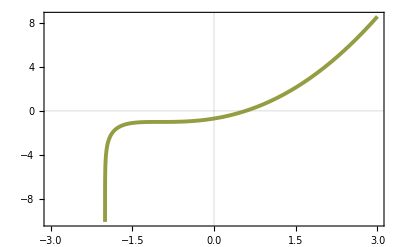

```mathematica
Clear[x,y];
y[x_]=2 x+x^2-(x+1)Log[x+2];
Plot[y[x],{x,-3,3},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.4. Drawing Parametric Plots

Task. Build function . Build table of values on interval  and corresponding list plot.

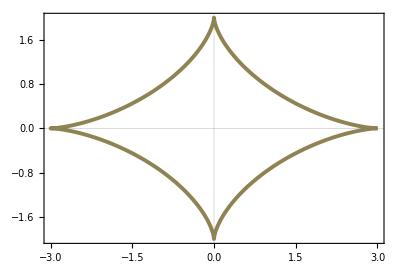

```mathematica
Remove[x,y,t];
x[t_]=3(Cos[t])^3;
y[t_]=2(Sin[t])^3;
p1=ParametricPlot[{x[t],y[t]},{t,0,2π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007],Blue},ColorFunction->"DarkRainbow"]
```

```mathematica
points=Table[{x[t],y[t]},{t,0,2π,π/8}];
npoints=N[points];
npoints//TableForm
```

3. | 0.
2.36574 | 0.112085
1.06066 | 0.707107
0.168128 | 1.57716
0. | 2.
-0.168128 | 1.57716
-1.06066 | 0.707107
-2.36574 | 0.112085
-3. | 0.
-2.36574 | -0.112085
-1.06066 | -0.707107
-0.168128 | -1.57716
0. | -2.
0.168128 | -1.57716
1.06066 | -0.707107
2.36574 | -0.112085
3. | 0.

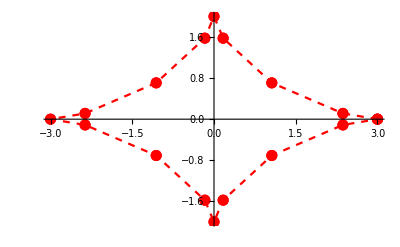

```mathematica
p2=ListPlot[npoints,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Red,Dashed}]
```

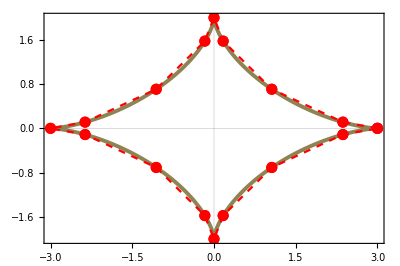

```mathematica
Show[p1,p2]
```

### 6.5. Drawing parametric plots

Task. Build plot  for interval .

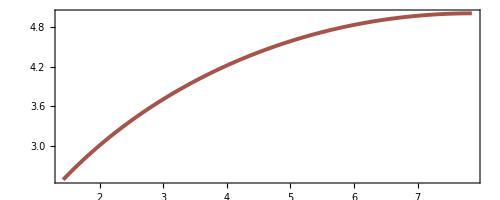

```mathematica
Clear[x,y,t]
x[t_]=5/2(t-Sin[t]);
y[t_]=5/2(1-Cos[t]);
p1=ParametricPlot[{x[t],y[t]},{t,π/2,π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

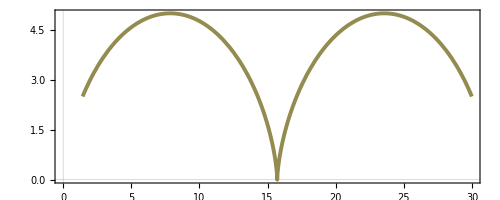

```mathematica
p2=ParametricPlot[{x[t],y[t]},{t,π/2,(7π)/2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.6. Build unexplicitly defined functions

Task. Build curve

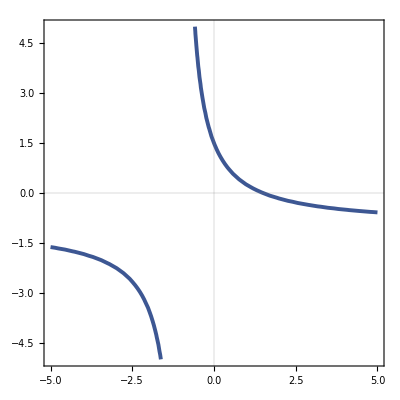

```mathematica
Remove[x,y,F];
F[x_,y_]=2x y+2x+2y-3;
ContourPlot[F[x,y]==0,{x,-5,5},{y,-5,5},PlotTheme->"Scientific",ColorFunction->"DarkRainbow",ContourStyle->{Thickness[0.007]}]
```

## 7. Geometric objects

### 7.1. Building a plane based on three points

Task: Write down an equation of plane intersecting points . Display this plane and three points.

```mathematica
Clear[A1,A2,A3,x,y,z];
A1={-3,-5,6};A2={2,1,-4};A3={0,-3,-1};
p1=ListPointPlot3D[{A1,A2,A3}->{"A_1","A_2","A_3"},PlotStyle->{Directive[PointSize[0.03],Red]}];
r={x,y,z};
Eq=Det[{r-A1,A2-A1,A3-A1}];
Print["Plane equation is ",Eq == 0]
```

Plane equation is 7-22 x+5 y-8 z==0

```mathematica
p2=ContourPlot3D[Eq==0,{x,-7,5},{y,-7,5},{z,-5,7},ContourStyle->Directive[Opacity[0.5],Blue]];
Show[p2,p1,PlotRange->All,AspectRatio->Automatic]
```

-Graphics3D-

### 7.2. Parallelogram in R^3

Task: In  three vertices of parallelogram  are given. Find coordinate of the fourth vertex  which is opposite to the side . Find area of this parallelogram. Display contours of this parallelogram and its vertices.

```mathematica
A1={6,2,-3};A2={6,3,-2};A3={7,3,-3};
A1A2=A2-A1;A1A3=A3-A1;
A4=A1+(A1A2+A1A3);
Print["Coordinate of vertex A_4 is ",A4]
```

Coordinate of vertex A_4 is {7,4,-2}

```mathematica
p1=Graphics3D[{Thickness[0.01],Line[{A1,A2,A4,A3,A1}]}];
p2=ListPointPlot3D[{A1,A2,A3,A4}->{"A_1","A_2","A_3","A_4"},PlotStyle->{Directive[PointSize[0.03],Red]}];
Show[p1,p2]
```

-Graphics3D-

```mathematica
S=Norm[Cross[A1A2,A1A3]];
Print["Area of this parallelogram is ",S]
```

Area of this parallelogram is √3

### 7.3. Calculations in R^3 triangle

Task: Given a triangle with vertices  find length of height  from vertex  on side . Find length of median  from vertex  on side . Display triangle’s contour and its median.

```mathematica
A1={-4,-2,0};
A2={-1,-2,4};
A3={3,-2,1};
p1=Graphics3D[{Thickness[0.02],Opacity[0.8],Black,Line[{A1,A2,A3,A1}]}]
```

-Graphics3D-

```mathematica
A1A2=A2-A1;A1A3=A3-A1;
S=1/2 Norm[Cross[A1A2,A1A3]];
Print["Area of this triangle is ",S]
```

Area of this triangle is 25/2

```mathematica
LengthA1A3=Norm[A1A3];
h=(2S)/LengthA1A3;
Print["Length of height is ", h]
```

Length of height is 5/(√2)

```mathematica
A2A1=A1-A2;
A2A3=A3-A2;
A2M=(A2A1+A2A3)/2;
LengthA2M=Norm[A2M];
Print["Length of median A_2M is ",LengthA2M]
```

Length of median A_2M is 5/(√2)

```mathematica
M=A2+A2M;
Print["Coordinate of median is ",M]
```

Coordinate of median is {-1/2,-2,1/2}

```mathematica
p2=Graphics3D[{Thickness[0.02],Black,Dashed,Opacity[1.0],Arrowheads[0.1],Arrow[{A2,M}]}];
p3=ListPointPlot3D[{A1,A2,A3,M}->{"A_1","A_2","A_3","M"},PlotStyle->{Directive[PointSize[0.03],Red]}];
Show[p1,p2,p3,Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### 7.4. Line and plane in R^3

Task: Find intersection point of line  and plane . Display plane, line, and intersection point.

```mathematica
Remove[x,y,z,t];
x[t_]=-2-t;
y[t_]=1+t;
z[t_]=-3+2t;
sol=Solve[x[t]+2y[t]+3z[t]-2 == 0,t];
t0=t/.sol[[1]];
Print["Parameter t at which plane and line intersect is ",t0]
```

Parameter t at which plane and line intersect is 11/7

```mathematica
G={x[t0],y[t0],z[t0]};
Print["Intersection point has coordinates ",G]
```

Intersection point has coordinates {-25/7,18/7,1/7}

```mathematica
pLine=ParametricPlot3D[{x[t],y[t],z[t]},{t,1.2,1.9},PlotStyle->{Red,Thickness[0.01],Dashed}];
pPlane=ContourPlot3D[x+2y+3z-2 == 0,{x,-4,-3},{y,2,3},{z,-1,2},ContourStyle->Directive[Blue,Opacity[0.8],Specularity[White,30]]];
pG=ListPointPlot3D[{G}->{"Intersection"},PlotStyle->{Directive[PointSize[0.03],Red]}];
Show[pLine,pPlane,pG,PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics3D-

## 8. Animations

### 8.1. Curve animation

Task: Build animation of curve  movement on the given time interval .

```mathematica
Remove[x,t];
Animate[
Plot[12x(x-t)^5 Sin[t],{x,0,1},PlotRange->{-200,1000},PlotLabel->Style["t="<>ToString[t],Blue,20],PlotTheme->"Scientific",PlotStyle->{Thickness[0.007],Blue}],
{t,0,2π},AnimationRunning->False
]
```

### 8.2. Animation of point movement along the curve

Task: Build point’s movement animation along the curve .

```mathematica
Remove[x,y,t];
x[t_]=5/2(t-Sin[t]);
y[t_]=5/2(1-Cos[t]);
Animate[
Show[
ParametricPlot[{x[τ],y[τ]},{τ,0,3π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007],Blue}],
ListPlot[{{x[t],y[t]}}->{"Point"},PlotStyle->{Black,PointSize[0.03]}],
GridLines->Automatic],
{t,0,3π}]
```